# Unit Step

info@cafeplanck.com

```mathematica
UnitStep[x]//TraditionalForm
```

x

```mathematica
PiecewiseExpand[UnitStep[x],-3<x<3]
```

Piecewise[{{1, x≥0}, {0, True}}]

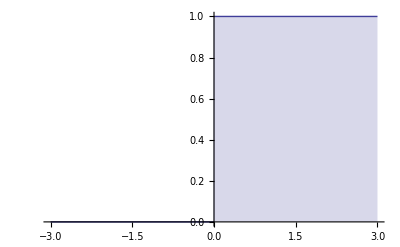

```mathematica
Plot[UnitStep[x],{x,-3,3},Filling->Axis]
```

```mathematica
UnitStep[x,y]//TraditionalForm
```

x,y

```mathematica
PiecewiseExpand[UnitStep[x,y]]
```

Piecewise[{{1, x≥0&&y≥0}, {0, True}}]

```mathematica
Plot3D[UnitStep[x,y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

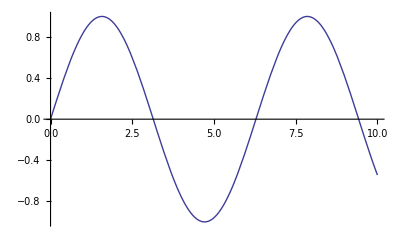

```mathematica
Plot[Sin[x],{x,0,10}]
```

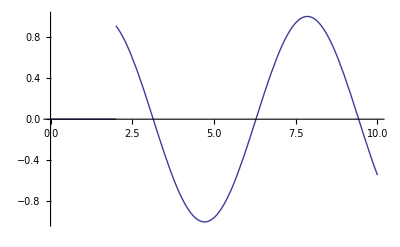

```mathematica
Plot[UnitStep[x-2] Sin[x],{x,0,10}]
```

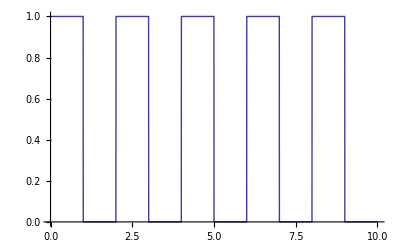

```mathematica
Plot[UnitStep[Sin[π x]],{x,0,10},Exclusions->None]
```